```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
```

```mathematica
data=ReadList["/home/cplumber/CausalChargeDiffusion/largek_1F1.test",Number];
len=Length[data]
```

321600

```mathematica
a=data[[Range[1,len,8]]]+I data[[Range[2,len,8]]];
b=data[[Range[3,len,8]]]+I data[[Range[4,len,8]]];
z=data[[Range[5,len,8]]]+I data[[Range[6,len,8]]];
result=data[[Range[7,len,8]]]+I data[[Range[8,len,8]]];
```

```mathematica
comparison={result,Hypergeometric1F1[a,b,z]}//Transpose;
```

2.0253×10^-15

2.35507×10^-30

8.14169×10^-11

2.59565×10^-25

{0.,1.80099×10^-14}

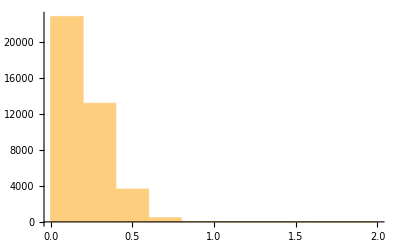

```mathematica
residuals=2 Abs[comparison[[;;,1]]-comparison[[;;,2]]]/Abs[comparison[[;;,1]]+comparison[[;;,2]]];
Mean[residuals]
Variance[residuals]
Total[residuals]
Total[residuals^2]
{Min[residuals],Max[residuals]}
Histogram[residuals]
```